```mathematica
Reverse[CycleBaseCoeff[ChromaticPolynomial[PetersenGraph[],x]]]
```

{0,-84,60,10,-56,58,-35,15,-5,1}

```mathematica
FindGeneratingFunction[{0,-84,60,10,-56,58,-35,15,-5,1},x]
```

FindGeneratingFunction[{0,-84,60,10,-56,58,-35,15,-5,1},x]

```mathematica
Table[ChromaticPolynomial[CycleGraph[k],4],{k,1,10}]/12
```

{0,1,2,7,20,61,182,547,1640,4921}

```mathematica
ChromaticPolynomial[PetersenGraph[],4]
```

12960

```mathematica
Sum[Reverse[CycleBaseCoeff[ChromaticPolynomial[PetersenGraph[],x]]][[k]]*ChromaticPolynomial[CycleGraph[k],4],{k,1,10}]
```

12960

```mathematica
ChromaticPolynomial[PathGraph[Range[11]],x]
```

x-10 x^2+45 x^3-120 x^4+210 x^5-252 x^6+210 x^7-120 x^8+45 x^9-10 x^10+x^11

```mathematica
Ratios[Table[ChromaticPolynomial[CycleGraph[k],3],{k,1,20}]]//N
```

Divide::infy: Infinite expression 6/0 encountered.

{ComplexInfinity,1.,3.,1.66667,2.2,1.90909,2.04762,1.97674,2.01176,1.99415,2.00293,1.99854,2.00073,1.99963,2.00018,1.99991,2.00005,1.99998,2.00001}

```mathematica
Ratios[Table[ChromaticPolynomial[CycleGraph[k],4],{k,1,20}]]//N
```

Divide::infy: Infinite expression 12/0 encountered.

{ComplexInfinity,2.,3.5,2.85714,3.05,2.98361,3.00549,2.99817,3.00061,2.9998,3.00007,2.99998,3.00001,3.,3.,3.,3.,3.,3.}

```mathematica
PathPoly[n_]:=PathPoly[n]=ChromaticPolynomial[PathGraph[Range[n]],x]
```

```mathematica
PathBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥2,pos--,
current = PathPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
result
]
```

```mathematica
PathBaseCoeff[ChromaticPolynomial[PetersenGraph[],x]]
```

{1,-6,21,-56,114,-170,180,-120,36,0}

```mathematica
CycleBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = CyclePoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
result
]
```

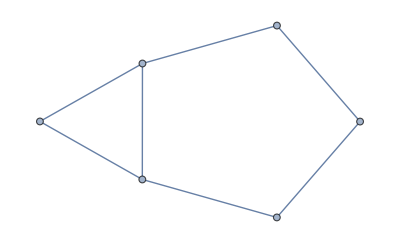
{{1,-1,0,0,-1,0,0},-Graphics-}

```mathematica
With[
{g=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,3<->1}]},
{CycleBaseCoeff[ChromaticPolynomial[g,x]],g}
]
```

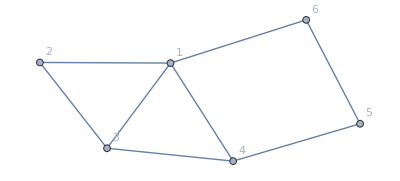

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,3<->1,4<->1}, VertexLabels->"Name"]
```

```mathematica
CycleBaseCoeff[ChromaticPolynomial[JacobsThalGraph[1],x]]
```

{1,-4,3,4,0,0}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[JacobsThalGraph[2],x]]
```

{1,-6,13,-5,-14,0,0}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[JacobsThalGraph[3],x]]
```

{1,-8,26,-35,-1,43,0,0}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[JacobsThalGraph[4],x]]
```

{1,-10,43,-91,75,44,-119,0,0}

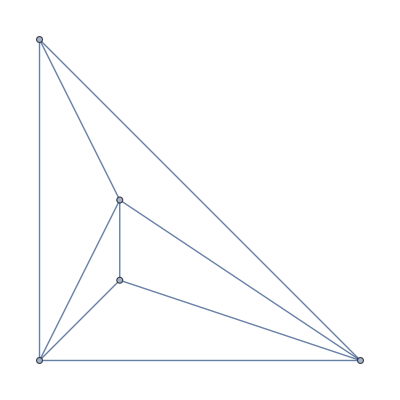

```mathematica
Graph[JacobsThalGraph[1],GraphLayout->"PlanarEmbedding"]
```

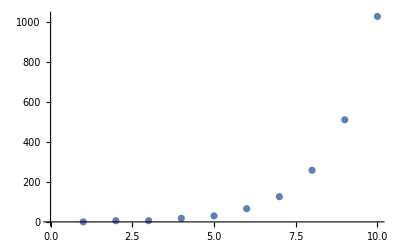

```mathematica
ListPlot[Table[ChromaticPolynomial[CycleGraph[k],3],{k,1,10}]]
```

```mathematica
FindGeneratingFunction[Table[ChromaticPolynomial[CycleGraph[k],3],{k,1,10}],x]
```

-(6 x)/(-1+x+2 x^2)

```mathematica
FindGeneratingFunction[Table[ChromaticPolynomial[CycleGraph[k],4],{k,1,10}],x]
```

-(12 x)/(-1+2 x+3 x^2)

```mathematica
FindGeneratingFunction[Table[ChromaticPolynomial[CycleGraph[k],5],{k,1,10}],x]
```

-(20 x)/(-1+3 x+4 x^2)

```mathematica
FindGeneratingFunction[Table[ChromaticPolynomial[CycleGraph[k],6],{k,1,10}],x]
```

-(30 x)/(-1+4 x+5 x^2)

```mathematica
FindGeneratingFunction[Table[ChromaticPolynomial[CycleGraph[k],7],{k,1,10}],x]
```

-(42 x)/(-1+5 x+6 x^2)

```mathematica
FindGeneratingFunction[Table[ChromaticPolynomial[CycleGraph[k],8],{k,1,10}],x]
```

-(56 x)/(-1+6 x+7 x^2)

```mathematica
FindGeneratingFunction[Table[ChromaticPolynomial[CompleteGraph[k],8],{k,1,10}],x]
```

```mathematica
FindGeneratingFunction[{8,56,336,1680,6720,20160,40320,40320},x]
```

FindGeneratingFunction[{8,56,336,1680,6720,20160,40320,40320},x]

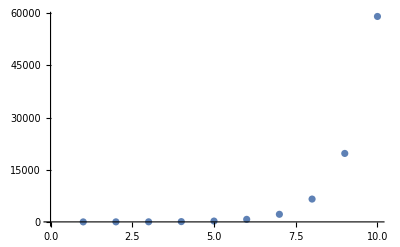

```mathematica
ListPlot[Table[ChromaticPolynomial[CycleGraph[k],4],{k,1,10}]]
```

```mathematica
Table[ChromaticPolynomial[CycleGraph[k],4],{k,1,10}]
```

{0,12,24,84,240,732,2184,6564,19680,59052}

```mathematica
nn=28;CoefficientList[Series[(12 x^2)/((x+1)^2 (1-(4 x)/(x+1)))+4 x+1,{x,0,nn}],x]
```

{1,4,12,24,84,240,732,2184,6564,19680,59052,177144,531444,1594320,4782972,14348904,43046724,129140160,387420492,1162261464,3486784404,10460353200,31381059612,94143178824,282429536484,847288609440,2541865828332,7625597484984,22876792454964}

```mathematica
deps1
```

{{0,1,{1,<1,2,3>}},{1,2,{1,<1,2,4>}},{2,3,{1,<2,3,4>}},{3,5,{1,<1,2,5>}},{3,8,{1,<1,3,5>}},{3,9,{1,<2,3,6>}},{4,6,{1,<2,3,4>}},{5,13,{1,<3,4,5>}},{5,16,{1,<2,3,6>}},{5,12,{1,<3,4,6>}},{5,17,{1,<2,5,6>}},{5,10,{1,<4,5,6>}},{6,20,{1,<1,3,5>}},{6,14,{1,<3,4,5>}},{6,19,{1,<1,2,7>}},{6,15,{1,<1,5,7>}},{7,11,{1,<1,2,5>}},{8,13,{1,<1,2,5>}},{8,22,{1,<1,3,5>}},{8,16,{1,<2,3,7>}},{9,17,{1,<1,2,5>}},{9,16,{1,<1,3,5>}},{9,23,{1,<2,5,6>}},{10,32,{1,<2,3,6>}},{10,29,{1,<4,5,6>}},{10,27,{1,<1,2,7>}},{10,33,{1,<2,5,7>}},{10,28,{1,<1,3,7>}},{10,34,{1,<3,5,7>}},{11,42,{1,<2,3,6>}},{11,43,{1,<3,4,6>}},{11,44,{1,<2,5,6>}},{11,31,{1,<4,5,6>}},{11,26,{1,<1,2,7>}},{11,45,{1,<2,5,7>}},{11,39,{1,<1,3,7>}},{12,51,{1,<2,3,6>}},{12,50,{1,<3,4,6>}},{12,52,{1,<2,5,6>}},{12,28,{1,<1,2,7>}},{12,33,{1,<2,5,7>}},{12,48,{1,<1,3,7>}},{12,53,{1,<3,5,7>}},{13,54,{1,<3,4,5>}},{13,47,{1,<3,4,6>}},{13,24,{1,<4,5,6>}},{13,29,{1,<1,2,7>}},{13,58,{1,<2,5,7>}},{13,50,{1,<1,3,7>}},{13,59,{1,<3,5,7>}},{13,60,{1,<2,3,8>}},{13,53,{1,<3,6,8>}},{13,61,{1,<2,5,8>}},{13,34,{1,<5,6,8>}},{14,57,{1,<3,4,5>}},{14,25,{1,<4,5,6>}},{14,30,{1,<1,2,7>}},{14,63,{1,<2,5,7>}},{14,64,{1,<2,3,8>}},{14,49,{1,<2,6,8>}},{14,35,{1,<4,6,8>}},{15,49,{1,<3,4,5>}},{15,65,{1,<2,3,6>}},{15,25,{1,<4,5,6>}},{15,66,{1,<2,6,8>}},{15,67,{1,<5,6,8>}},{16,60,{1,<3,4,5>}},{16,51,{1,<3,4,6>}},{16,69,{1,<2,5,6>}},{16,32,{1,<4,5,6>}},{16,34,{1,<1,2,7>}},{16,70,{1,<2,5,7>}},{16,53,{1,<1,3,7>}},{16,71,{1,<3,5,7>}},{16,68,{1,<2,3,8>}},{16,61,{1,<2,6,8>}},{17,61,{1,<3,4,5>}},{17,69,{1,<2,3,6>}},{17,52,{1,<3,4,6>}},{17,32,{1,<4,5,6>}},{17,33,{1,<1,2,7>}},{17,70,{1,<2,5,7>}},{18,38,{1,<2,3,6>}},{18,36,{1,<3,4,6>}},{19,67,{1,<2,3,6>}},{19,35,{1,<4,5,6>}},{20,64,{1,<3,4,5>}},{20,65,{1,<2,3,6>}},{20,57,{1,<3,4,6>}},{20,67,{1,<1,2,7>}},{21,37,{1,<1,2,5>}},{22,54,{1,<1,2,5>}},{22,73,{1,<1,3,5>}},{22,59,{1,<2,3,7>}},{22,68,{1,<3,6,7>}},{23,69,{1,<1,2,5>}},{24,77,{1,<4,5,6>}},{24,74,{1,<1,2,7>}},{24,83,{1,<2,5,7>}},{24,75,{1,<1,3,7>}}}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ReadGrof[22],x]]
```

{1,-10,39,-70,40,48,-80,0}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ReadGrof[59],x]]
```

{1,-12,59,-148,180,-32,-176,192,0}

```mathematica
Sum[Reverse[CycleBaseCoeff[ChromaticPolynomial[ReadGrof[22],x]]][[k]]*ChromaticPolynomial[CycleGraph[k],4],{k,1,8}]
```

24

```mathematica
Sum[Reverse[CycleBaseCoeff[ChromaticPolynomial[ReadGrof[59],x]]][[k]]*ChromaticPolynomial[CycleGraph[k],4],{k,1,9}]
```

24

```mathematica
TableForm[FactorInteger[Table[ChromaticPolynomial[CycleGraph[k],4]/12,{k,1,100}]],TableDepth->1]
```

{{0,1}}
{{1,1}}
{{2,1}}
{{7,1}}
{{2,2},{5,1}}
{{61,1}}
{{2,1},{7,1},{13,1}}
{{547,1}}
{{2,3},{5,1},{41,1}}
{{7,1},{19,1},{37,1}}
{{2,1},{11,2},{61,1}}
{{67,1},{661,1}}
{{2,2},{5,1},{7,1},{13,1},{73,1}}
{{398581,1}}
{{2,1},{547,1},{1093,1}}
{{7,1},{31,1},{61,1},{271,1}}
{{2,4},{5,1},{17,1},{41,1},{193,1}}
{{103,1},{307,1},{1021,1}}
{{2,1},{7,1},{13,1},{19,1},{37,1},{757,1}}
{{2851,1},{101917,1}}
{{2,2},{5,2},{11,2},{61,1},{1181,1}}
{{7,2},{43,1},{547,1},{2269,1}}
{{2,1},{23,1},{67,1},{661,1},{3851,1}}
{{23535794707,1}}
{{2,3},{5,1},{7,1},{13,1},{41,1},{73,1},{6481,1}}
{{61,1},{151,1},{22996651,1}}
{{2,1},{398581,1},{797161,1}}
{{7,1},{19,1},{37,1},{19441,1},{19927,1}}
{{2,2},{5,1},{29,1},{547,1},{1093,1},{16493,1}}
{{523,1},{6091,1},{5385997,1}}
{{2,1},{7,1},{11,2},{13,1},{31,1},{61,1},{271,1},{4561,1}}
{{6883,1},{22434744889,1}}
{{2,5},{5,1},{17,1},{41,1},{193,1},{21523361,1}}
{{7,1},{67,1},{661,1},{25411,1},{176419,1}}
{{2,1},{103,1},{307,1},{1021,1},{1871,1},{34511,1}}
{{61,1},{547,1},{374857981681,1}}
{{2,2},{5,1},{7,1},{13,1},{19,1},{37,1},{73,1},{757,1},{530713,1}}
{{18427,1},{107671,1},{56737873,1}}
{{2,1},{1597,1},{2851,1},{101917,1},{363889,1}}
{{7,1},{79,1},{157,1},{2887,1},{10141,1},{398581,1}}
{{2,3},{5,2},{11,2},{41,1},{61,1},{1181,1},{42521761,1}}
{{33703,1},{270547105429567,1}}
{{2,1},{7,2},{13,1},{43,1},{547,1},{1093,1},{2269,1},{368089,1}}
{{82064241848634269407,1}}
{{2,2},{5,1},{23,1},{67,1},{661,1},{3851,1},{5501,1},{570461,1}}
{{7,1},{19,1},{31,1},{37,1},{61,1},{271,1},{387631,1},{755551,1}}
{{2,1},{47,1},{1001523179,1},{23535794707,1}}
{{16921,1},{256057,1},{1534179947851,1}}
{{2,4},{5,1},{7,1},{13,1},{17,1},{41,1},{73,1},{97,1},{193,1},{577,1},{769,1},{6481,1}}
{{547,1},{857643277,1},{127522693159,1}}
{{2,1},{11,2},{61,1},{151,1},{8951,1},{391151,1},{22996651,1}}
{{7,1},{103,1},{307,1},{613,1},{1021,1},{30091,1},{129159847,1}}
{{2,2},{5,1},{53,1},{398581,1},{797161,1},{4795973261,1}}
{{78719947,1},{61557605176233223,1}}
{{2,1},{7,1},{13,1},{19,1},{37,1},{109,1},{433,1},{757,1},{8209,1},{19441,1},{19927,1}}
{{61,1},{67,1},{661,1},{659671,1},{24472341743191,1}}
{{2,3},{5,1},{29,1},{41,1},{547,1},{1093,1},{16493,1},{430697,1},{647753,1}}
{{7,1},{2851,1},{3079,1},{53923,1},{101917,1},{1162320517,1}}
{{2,1},{59,1},{523,1},{6091,1},{28537,1},{5385997,1},{20381027,1}}
{{3187,1},{1108439448677340328268341,1}}
{{2,2},{5,2},{7,1},{11,2},{13,1},{31,1},{61,1},{73,1},{271,1},{1181,1},{4561,1},{47763361,1}}
{{367,1},{86630432442539925437931403,1}}
{{2,1},{683,1},{6883,1},{102673,1},{4404047,1},{22434744889,1}}
{{7,2},{19,1},{37,1},{43,1},{127,1},{547,1},{883,1},{2269,1},{2521,1},{550554229,1}}
{{2,6},{5,1},{17,1},{41,1},{193,1},{21523361,1},{926510094425921,1}}
{{61,1},{398581,1},{105919308797935444986721,1}}
{{2,1},{7,1},{13,1},{23,1},{67,1},{661,1},{3851,1},{25411,1},{176419,1},{2413941289,1}}
{{5390821,1},{4299412981246169975118907,1}}
{{2,2},{5,1},{103,1},{307,1},{1021,1},{1871,1},{34511,1},{956353,1},{1743831169,1}}
{{7,1},{139,1},{5107,1},{9109,1},{132619,1},{1476463,1},{23535794707,1}}
{{2,1},{11,2},{61,1},{71,1},{547,1},{1093,1},{2664097031,1},{374857981681,1}}
{{853,1},{2131,1},{82219,1},{3099719989,1},{4052490063499,1}}
{{2,3},{5,1},{7,1},{13,1},{19,1},{37,1},{41,1},{73,1},{757,1},{6481,1},{530713,1},{282429005041,1}}
{{439,1},{38488154120055537150068589763279,1}}
{{2,1},{18427,1},{107671,1},{13097927,1},{56737873,1},{17189128703,1}}
{{7,1},{31,1},{61,1},{151,1},{271,1},{2551,1},{26251,1},{119101,1},{1530601,1},{22996651,1}}
{{2,2},{5,1},{1597,1},{2851,1},{101917,1},{363889,1},{5301533,1},{25480398173,1}}
{{67,1},{547,1},{661,1},{56495392933101222275861053369,1}}
{{2,1},{7,1},{13,2},{79,1},{157,1},{313,1},{2887,1},{6553,1},{7333,1},{10141,1},{398581,1},{797161,1}}
{{66361,1},{327220181191,1},{567239060331150635317,1}}
{{2,4},{5,2},{11,2},{17,1},{41,1},{61,1},{193,1},{1181,1},{14401,1},{42521761,1},{128653413121,1}}
{{7,1},{19,1},{37,1},{163,1},{1297,1},{19441,1},{19927,1},{208657,1},{224209,1},{5879415781,1}}
{{2,1},{83,1},{33703,1},{2526913,1},{86950696619,1},{270547105429567,1}}
{{499,1},{997,1},{2466097,1},{813201725710097952736361977,1}}
{{2,2},{5,1},{7,2},{13,1},{29,1},{43,1},{73,1},{547,1},{1093,1},{2269,1},{2857,1},{16493,1},{368089,1},{109688713,1}}
{{61,1},{103,1},{307,1},{1021,1},{1531,1},{224401,1},{13271362257832586268931,1}}
{{2,1},{431,1},{380808546861411923,1},{82064241848634269407,1}}
{{7,1},{349,1},{523,1},{6091,1},{142159,1},{261697,1},{1383301,1},{5385997,1},{37464463,1}}
{{2,3},{5,1},{23,1},{41,1},{67,1},{89,1},{661,1},{3851,1},{5501,1},{570461,1},{2382953,1},{56625998353,1}}
{{264331,1},{1125706177,1},{2444322641415331355533344283,1}}
{{2,1},{7,1},{11,2},{13,1},{19,1},{31,1},{37,1},{61,1},{181,1},{271,1},{757,1},{1621,1},{4561,1},{387631,1},{755551,1},{927001,1}}
{{547,1},{8737,1},{398581,1},{595141,1},{2354116499281,1},{2452788561133,1}}
{{2,2},{5,1},{47,1},{12553493,1},{1001523179,1},{23535794707,1},{70601370627701,1}}
{{7,1},{373,1},{6883,1},{541447,1},{3058399,1},{22434744889,1},{88239050462461,1}}
{{2,1},{1223,1},{16921,1},{21997,1},{256057,1},{5112661,1},{96656723,1},{1534179947851,1}}
{{61,1},{2851,1},{39901,1},{101917,1},{29574984661,1},{25349956307509384561,1}}
{{2,5},{5,1},{7,1},{13,1},{17,1},{41,1},{73,1},{97,1},{193,1},{577,1},{769,1},{6481,1},{76801,1},{21523361,1},{24127552321,1}}
{{459991849,1},{503803759819,1},{20591603926857377806745611,1}}
{{2,1},{491,1},{547,1},{1093,1},{4019,1},{8233,1},{51157,1},{131713,1},{857643277,1},{127522693159,1}}
{{7,1},{19,1},{37,1},{67,1},{199,1},{397,1},{661,1},{4357,1},{25411,1},{176419,1},{337448233,1},{378450588583,1}}

```mathematica
CycleBaseCoeffForGrof[k_]:=CycleBaseCoeff[ChromaticPolynomial[ReadGrof[k],x]]
```

```mathematica
CycleBaseCoeff[ChromaticPolynomial[CompleteGraph[3],x]]
```

{1,0,0}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[CompleteGraph[4],x]]
```

{1,-2,-1,0}

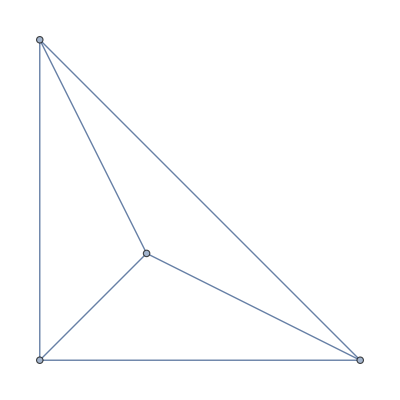

```mathematica
Graph[CompleteGraph[4],GraphLayout->"PlanarEmbedding"]
```

```mathematica
TableForm[Map[{CycleBaseCoeffForGrof[#[[1]]],CycleBaseCoeffForGrof[#[[2]]]}&,Rest[deps1]],TableDepth->1]
```

{{1,-2,-1,0,0},{1,-4,3,4,0,0}}
{{1,-4,3,4,0,0},{1,-6,11,-2,-12,0,0}}
{{1,-6,11,-2,-12,0,0},{1,-8,23,-24,-8,32,0,0}}
{{1,-6,11,-2,-12,0,0},{1,-8,23,-24,-8,32,0,0}}
{{1,-6,11,-2,-12,0,0},{1,-8,23,-24,-8,32,0,0}}
{{1,-6,13,-5,-14,0,0},{1,-8,25,-31,-4,39,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,25,-31,-4,39,0,0},{1,-10,41,-81,58,47,-100,0,0}}
{{1,-8,25,-31,-4,39,0,0},{1,-10,41,-81,58,47,-100,0,0}}
{{1,-8,25,-31,-4,39,0,0},{1,-10,41,-81,58,47,-100,0,0}}
{{1,-8,25,-31,-4,39,0,0},{1,-10,41,-81,58,47,-100,0,0}}
{{1,-8,26,-35,-1,43,0,0},{1,-10,42,-87,69,45,-112,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-8,23,-24,-8,32,0,0},{1,-10,39,-70,40,48,-80,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,42,-87,69,45,-112,0,0},{1,-12,62,-171,243,-93,-202,276,0,0}}
{{1,-10,42,-87,69,45,-112,0,0},{1,-12,62,-171,243,-93,-202,276,0,0}}
{{1,-10,42,-87,69,45,-112,0,0},{1,-12,62,-171,243,-93,-202,276,0,0}}
{{1,-10,42,-87,69,45,-112,0,0},{1,-12,62,-171,243,-93,-202,276,0,0}}
{{1,-10,42,-87,69,45,-112,0,0},{1,-12,62,-171,243,-93,-202,276,0,0}}
{{1,-10,42,-87,69,45,-112,0,0},{1,-12,62,-171,243,-93,-202,276,0,0}}
{{1,-10,42,-87,69,45,-112,0,0},{1,-12,62,-171,243,-93,-202,276,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,43,-95,87,39,-131,0,0},{1,-12,63,-181,277,-135,-209,328,0,0}}
{{1,-10,43,-95,87,39,-131,0,0},{1,-12,63,-181,277,-135,-209,328,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,41,-81,58,47,-100,0,0},{1,-12,61,-163,220,-69,-194,244,0,0}}
{{1,-10,43,-91,75,44,-119,0,0},{1,-12,63,-177,257,-106,-207,295,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-10,39,-70,40,48,-80,0,0},{1,-12,59,-148,180,-32,-176,192,0,0}}
{{1,-12,59,-148,180,-32,-176,192,0,0},{1,-14,83,-266,476,-392,-112,544,-448,0,0}}
{{1,-12,59,-148,180,-32,-176,192,0,0},{1,-14,83,-266,476,-392,-112,544,-448,0,0}}
{{1,-12,59,-148,180,-32,-176,192,0,0},{1,-14,83,-266,476,-392,-112,544,-448,0,0}}
{{1,-12,59,-148,180,-32,-176,192,0,0},{1,-14,83,-266,476,-392,-112,544,-448,0,0}}